## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSFittingPackage`"];
Get["MASSFittingPackage`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="PFK1";
KeqEquilibrator=1;

(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/MASS_fitting_package/";

mainFolder = "test_refactor_PFK1";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder];
```

/home/mrama/Dropbox/MASS_fitting_package/data

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.xls"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.xls"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.xls"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

### Construct enzyme module

```mathematica
catalyticBranch={"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&f6p&atp",
				"E_PFK1[c] + atp[c] <=> E_PFK1[c]&atp",
				"E_PFK1[c]&atp + f6p[c] <=> E_PFK1[c]&atp&f6p",
				"E_PFK1[c]&f6p&atp <=> E_PFK1[c]&fdp&adp",
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&adp + fdp[c]",
				"E_PFK1[c]&adp <=> E_PFK1[c] + adp[c]",
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["gdp","c"], m["adp","c"]},ActivationSites->1,Inhibitors->{m["pep","c"]},InhibitionSites->1];
```

```mathematica
enzymeModel["Reactions"]
```

{((PFK1^c)_^+atp^c⇌(PFK1^c&atp^c)_^)^PFK11,((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK12,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK13,((PFK1^c&adp^c)_^⇌(PFK1^c)_^+adp^c)^PFK14,((PFK1^c&atp^c)_^+f6p^c⇌(PFK1^c&atp^c&f6p^c)_^)^PFK15,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK16,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK17,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&adp^c)_^+fdp^c)^PFK18,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK19,((PFK1^c)_^(adp^c)+atp^c⇌(PFK1^c&atp^c)_^(adp^c))^PFK11$32,((PFK1^c)_^(adp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(adp^c))^PFK12$32,((PFK1^c&fdp^c)_^(adp^c)⇌(PFK1^c)_^(adp^c)+fdp^c)^PFK13$32,((PFK1^c&adp^c)_^(adp^c)⇌(PFK1^c)_^(adp^c)+adp^c)^PFK14$32,((PFK1^c&atp^c)_^(adp^c)+f6p^c⇌(PFK1^c&atp^c&f6p^c)_^(adp^c))^PFK15$32,((PFK1^c&f6p^c)_^(adp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(adp^c))^PFK16$32,((PFK1^c&fdp^c&adp^c)_^(adp^c)⇌(PFK1^c&fdp^c)_^(adp^c)+adp^c)^PFK17$32,((PFK1^c&fdp^c&adp^c)_^(adp^c)⇌(PFK1^c&adp^c)_^(adp^c)+fdp^c)^PFK18$32,((PFK1^c&f6p^c&atp^c)_^(adp^c)⇌(PFK1^c&fdp^c&adp^c)_^(adp^c))^PFK19$32,((PFK1^c)_^(gdp^c)+atp^c⇌(PFK1^c&atp^c)_^(gdp^c))^PFK11$33,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK12$33,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK13$33,((PFK1^c&adp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+adp^c)^PFK14$33,((PFK1^c&atp^c)_^(gdp^c)+f6p^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^c))^PFK15$33,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK16$33,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK17$33,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&adp^c)_^(gdp^c)+fdp^c)^PFK18$33,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK19$33,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$34,((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$35,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$36,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_adp", fbp^c->0}};

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFluxNoProdInhib=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, "NoProdInhibRefactor"];
```

```mathematica
{enzymeModel, nonCatalyticReactions} =addInhibitionReactions[enzymeModel, rxnName, {inhibitionList[[2]]},  allCatalyticReactions, nonCatalyticReactions];
nonCatalyticReactions//TableForm
```

((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$12
((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$13
((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep
((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp
((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_2_atp

```mathematica
(* get flux equation including inhibitions*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];

(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions];
eqRateConstSub={};


{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub, absoluteFluxNoProdInhib, absoluteFluxNoProdInhib,
Null, otherMetsReverseZeroSub];

(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal,
															Null, otherAbsoluteRatesReverse];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub, Null, otherAbsoluteRatesReverse];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={8.5,30};
(*Km data*)
kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			      logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];

(*kcat data*)
kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			   fileList, KeqEquilibrator];

(*S05 data*)
s05FittingData = simulateS05Data[rxn, metsFull, metSatForSub, metSatRevSub, s05List, otherParmsList, assumedSaturatingConc, eTotal,
			          logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, Null,bigg2equilibrator];

(*Keq data*)
haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];

(*L0 data*)
param = "L0";
L0Value =getOtherParamsValue[param, otherParmsList];
L0Ratio = getAllostericTransitionRatio[enzymeModel, nonCatalyticReactions];

{L0FittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[L0Ratio,L0Value, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="L0Ratio"];

(*ADP C inhibition data*)

logStepSize=0.5;
inhibFittingDataAdp=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  {inhibitionList[[2]]}, kmList, assumedSaturatingConc, eTotal, logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];

(*PEP NC inhibition data *)

inhibitor=m["pep","c"];
inhibRatio = getRatio[enzymeModel, inhibitor];
inhibVal=Select[inhibitionList,#[[2]]==getID@inhibitor&][[1]][[3]];

{inhibRatioFittingDataPep, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[inhibRatio,inhibVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="pep_inhibRatio"];


(*ADP inhibition data*)

logStepSize=0.5;
inhibFittingDataAdp=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  {inhibitionList[[2]]}, kmList, assumedSaturatingConc, eTotal, logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];

(*GDP activation data - to do *)
activator=m["gdp","c"];
actRatio = getRatio[enzymeModel, activator];
actVal=Select[activationList,#[[2]]==getID@activator&][[1]][[3]];

{actRatioFittingDataGdp, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[actRatio,actVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="gdp_actRatio"];

(*ADP activation data - to do *)
(*activator=m["adp","c"];
actRatio = getRatio[enzymeModel, activator];
actVal=Select[activationList,#[[2]]==getID@activator&][[1]][[3]];

{actRatioFittingDataGdp, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[actRatio,actVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="gdp_actRatio"];*)
```

{0.073096}

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData, s05FittingData, kcatFittingData, KeqFittingData, L0FittingData,inhibFittingDataAdp,inhibRatioFittingDataPep, actRatioFittingDataGdp}, 1];

dataPath =FileNameJoin[{inputPath,rxnName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath];
```

Keq_PFK1	adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	9.000000000000007e-6	0.001	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt	0.09090909090909098
1	0	0.000028460498941515435	0.001	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt	0.2402530733520423
1	0	0.00009000000000000007	0.001	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt	0.5000000000000002
1	0	0.00028460498941515434	0.001	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt	0.759746926647958
1	0	0.0009000000000000007	0.001	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt	0.9090909090909093
214110.97423935533	0	0.001	9.000000000000007e-6	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt	0.007702679340006974
214110.97423935533	0	0.001	0.000028460498941515435	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt	0.08097095080544874
214110.97423935533	0	0.001	0.00009000000000000007	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt	0.5000000000000004
214110.97423935533	0	0.001	0.00028460498941515434	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt	0.9190290491945515
214110.97423935533	0	0.001	0.0009000000000000007	0	0.01	0.01	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt	0.992297320659993
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0.01	0.01	0	0	0	1	8.5	30.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt	110.7
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt	1
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt	4.e6
1	0.0001	9.000000000000007e-6	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.06250000000000004
1	0.0001	0.000028460498941515435	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.17411239489546843
1	0.0001	0.00009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.40000000000000013
1	0.0001	0.00028460498941515434	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.6782688399674106
1	0.0001	0.0009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.8695652173913043
1	0.0002	9.000000000000007e-6	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.04761904761904766
1	0.0002	0.000028460498941515435	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.1365270594958144
1	0.0002	0.00009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.33333333333333354
1	0.0002	0.00028460498941515434	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.612574113277207
1	0.0002	0.0009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.8333333333333336
1	0.0004	9.000000000000007e-6	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.03225806451612906
1	0.0004	0.000028460498941515435	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.09535767393826003
1	0.0004	0.00009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.25000000000000017
1	0.0004	0.00028460498941515434	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.5131670194948621
1	0.0004	0.0009000000000000007	0.01	0	0.01	0.01	1	8.5	28.	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt	0.7692307692307694
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt	0.00075
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004
1	0	0	0	0	0	0	1	8.5	30	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt	0.00004

## Configure the Particle Swarm Optimization

```mathematica
numTrials=5;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	20
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateRev.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateRev_adp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateRev_fdp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt]
data_file_name	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/PFK1.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/output/raw/summary.txt
ultimate_result_name	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/output/raw/psoResults.txt

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound];
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	20
candidates_import_path	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/output/raw/psoResults.txt
candidates_export_path	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/output/raw/lmaResults.txt
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateFor.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/absRateRev.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_atp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateFor_f6p.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateRev_adp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/relRateRev_fdp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/prod_inhib_adp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/haldaneRatio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/L0Ratio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/pep_inhibRatio.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/gdp_actRatio.txt]
data_file_name	/home/mrama/Dropbox/Kinetics/Enzymes_new/PFK1/test_refactor_PFK1/input/PFK1.dat
value_row	-1
function_row	-2
data_row_high	-2

### Make the shell script to run pso and lma fitting methods

```mathematica
runFitScriptPath="/home/mrama/Dropbox/Kinetics/Scripts/run_fit_rel.py"
shRunFit=createCombinedFitShellScript[runFitScriptPath, psoParameterPath, lmaParameterPath, psoTrialSummaryFileName, psoResultsFileName, lmaResultsFileName, numTrials, dataPath];

shRunFitPath=FileNameJoin[{inputPath,"runFit.sh"}, OperatingSystem->$OperatingSystem];
Export[shRunFitPath,shRunFit,"Table"];

(*Make the Shell Script Executable*)
mkShRunFitExec="chmod u+x "<> shRunFitPath;
mkShRunFitExecCmd="!"<>mkShRunFitExec<>" 2>&1";
Import[mkShRunFitExecCmd,"Text"];
```

/home/mrama/Dropbox/Kinetics/Scripts/run_fit_rel.py

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothCmd="cd "<>inputPath<>" && ./"<>"runFit.sh";
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

best_fit: 5.20214971656
best_fit: 11.3530198528
best_fit: 8.03050813666
best_fit: 2.71457695991
best_fit: 10.3974864859

#### Run the PSO Algorithm Independently - not working

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/GAPD_dKd/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently - not working

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[FileNameJoin[{inputPath , "PFK.dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw", "lmaResults.txt"}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
prod_inhib_glyc3p | 52.0945 | 0.0625 | 0.0950591
prod_inhib_glyc3p | 40.4472 | 0.174112 | 0.244536
prod_inhib_glyc3p | 21.526 | 0.4 | 0.486104
prod_inhib_glyc3p | 3.9343 | 0.678269 | 0.704954
prod_inhib_glyc3p | 6.44477 | 0.869565 | 0.813524
prod_inhib_glyc3p | 74.6298 | 0.047619 | 0.083157
prod_inhib_glyc3p | 60.4322 | 0.136527 | 0.219033
prod_inhib_glyc3p | 35.8854 | 0.333333 | 0.452951
prod_inhib_glyc3p | 11.3432 | 0.612574 | 0.68206
prod_inhib_glyc3p | 3.55861 | 0.833333 | 0.803678
prod_inhib_glyc3p | 106.161 | 0.0322581 | 0.0665036
prod_inhib_glyc3p | 90.0551 | 0.0953577 | 0.181232
prod_inhib_glyc3p | 59.4337 | 0.25 | 0.398584
prod_inhib_glyc3p | 24.8053 | 0.513167 | 0.64046
prod_inhib_glyc3p | 2.00907 | 0.769231 | 0.784685
prod_inhib_glyc3p | 17.3592 | 0.0491493 | 0.0406174
prod_inhib_glyc3p | 23.9328 | 0.135972 | 0.10343
prod_inhib_glyc3p | 34.2924 | 0.308057 | 0.202417
prod_inhib_glyc3p | 43.486 | 0.513614 | 0.290264
prod_inhib_glyc3p | 48.3182 | 0.650976 | 0.336436
prod_inhib_glyc3p | 19.1964 | 0.0336788 | 0.0401439
prod_inhib_glyc3p | 5.90321 | 0.0948165 | 0.100414
prod_inhib_glyc3p | 14.1163 | 0.222603 | 0.19118
prod_inhib_glyc3p | 30.9937 | 0.387936 | 0.2677
prod_inhib_glyc3p | 39.5501 | 0.50702 | 0.306493
prod_inhib_glyc3p | 89.8089 | 0.0206677 | 0.0392292
prod_inhib_glyc3p | 60.643 | 0.0590629 | 0.0948805
prod_inhib_glyc3p | 20.1871 | 0.143172 | 0.172074
prod_inhib_glyc3p | 11.0517 | 0.260467 | 0.231681
prod_inhib_glyc3p | 25.9885 | 0.351541 | 0.260181
prod_inhib_nadp | 3.47733 | 0.0606061 | 0.0584986
prod_inhib_nadp | 5.05829 | 0.160169 | 0.152067
prod_inhib_nadp | 8.04581 | 0.333333 | 0.306514
prod_inhib_nadp | 12.4321 | 0.506498 | 0.44353
prod_inhib_nadp | 19.9952 | 0.606061 | 0.484877
prod_inhib_nadp | 8.6714 | 0.0454545 | 0.041513
prod_inhib_nadp | 5.44075 | 0.120127 | 0.113591
prod_inhib_nadp | 0.4384 | 0.25 | 0.251096
prod_inhib_nadp | 5.38268 | 0.379873 | 0.400321
prod_inhib_nadp | 2.0884 | 0.454545 | 0.464038
prod_inhib_nadp | 13.335 | 0.030303 | 0.0262621
prod_inhib_nadp | 5.82014 | 0.0800844 | 0.0754233
prod_inhib_nadp | 10.6473 | 0.166667 | 0.184412
prod_inhib_nadp | 32.2972 | 0.253249 | 0.335041
prod_inhib_nadp | 41.0117 | 0.30303 | 0.427308
prod_inhib_nadp | 40.3696 | 0.0625 | 0.037269
prod_inhib_nadp | 37.9254 | 0.174112 | 0.10808
prod_inhib_nadp | 32.3103 | 0.4 | 0.270759
prod_inhib_nadp | 23.8213 | 0.678269 | 0.516696
prod_inhib_nadp | 16.6341 | 0.869565 | 0.724921
prod_inhib_nadp | 22.7779 | 0.047619 | 0.0367724
prod_inhib_nadp | 21.805 | 0.136527 | 0.106757
prod_inhib_nadp | 19.5615 | 0.333333 | 0.268128
prod_inhib_nadp | 16.1481 | 0.612574 | 0.513655
prod_inhib_nadp | 13.2374 | 0.833333 | 0.723022
prod_inhib_nadp | 11.0355 | 0.0322581 | 0.0358179
prod_inhib_nadp | 9.28103 | 0.0953577 | 0.104208
prod_inhib_nadp | 5.20699 | 0.25 | 0.263017
prod_inhib_nadp | 1.06946 | 0.513167 | 0.507679
prod_inhib_nadp | 6.4971 | 0.769231 | 0.719253
prod_inhib_dhap | 16.055 | 0.0625 | 0.0524656
prod_inhib_dhap | 11.0709 | 0.174112 | 0.154837
prod_inhib_dhap | 0.669142 | 0.4 | 0.397323
prod_inhib_dhap | 4.73469 | 0.678269 | 0.710383
prod_inhib_dhap | 22.875 | 0.869565 | 0.670652
prod_inhib_dhap | 6.76662 | 0.047619 | 0.0508412
prod_inhib_dhap | 10.0636 | 0.136527 | 0.150267
prod_inhib_dhap | 16.1534 | 0.333333 | 0.387178
prod_inhib_dhap | 13.9675 | 0.612574 | 0.698136
prod_inhib_dhap | 20.1455 | 0.833333 | 0.665454
prod_inhib_dhap | 48.3384 | 0.0322581 | 0.0478511
prod_inhib_dhap | 48.7243 | 0.0953577 | 0.14182
prod_inhib_dhap | 47.2858 | 0.25 | 0.368215
prod_inhib_dhap | 31.4787 | 0.513167 | 0.674705
prod_inhib_dhap | 14.8179 | 0.769231 | 0.655247
prod_inhib_dhap | 51.0433 | 0.0529801 | 0.080023
prod_inhib_dhap | 40.9897 | 0.144739 | 0.204067
prod_inhib_dhap | 25.0869 | 0.32 | 0.400278
prod_inhib_dhap | 10.9132 | 0.518565 | 0.575157
prod_inhib_dhap | 3.44038 | 0.645161 | 0.667357
prod_inhib_dhap | 20.2507 | 0.0373832 | 0.0449535
prod_inhib_dhap | 20.5873 | 0.103566 | 0.124887
prod_inhib_dhap | 21.2629 | 0.235294 | 0.285325
prod_inhib_dhap | 22.085 | 0.393613 | 0.480542
prod_inhib_dhap | 22.6437 | 0.5 | 0.613219
prod_inhib_dhap | 0.354163 | 0.0235294 | 0.0234461
prod_inhib_dhap | 4.41757 | 0.0660105 | 0.0689265
prod_inhib_dhap | 15.8924 | 0.153846 | 0.178296
prod_inhib_dhap | 34.7323 | 0.265611 | 0.357863
prod_inhib_dhap | 52.2782 | 0.344828 | 0.525097
prod_inhib_nadph | 47.6586 | 0.0579011 | 0.0303062
prod_inhib_nadph | 44.9009 | 0.155173 | 0.0854986
prod_inhib_nadph | 39.6284 | 0.331034 | 0.199851
prod_inhib_nadph | 35.9221 | 0.515944 | 0.330606
prod_inhib_nadph | 43.6736 | 0.626632 | 0.352959
prod_inhib_nadph | 39.1148 | 0.0424779 | 0.0258627
prod_inhib_nadph | 39.0738 | 0.114592 | 0.0698166
prod_inhib_nadph | 39.3955 | 0.247423 | 0.149949
prod_inhib_nadph | 41.6259 | 0.390601 | 0.228009
prod_inhib_nadph | 48.9609 | 0.478088 | 0.244012
prod_inhib_nadph | 27.8389 | 0.0277136 | 0.0199984
prod_inhib_nadph | 32.1113 | 0.0752393 | 0.051079
prod_inhib_nadph | 39.1625 | 0.164384 | 0.100007
prod_inhib_nadph | 46.4805 | 0.262875 | 0.140689
prod_inhib_nadph | 53.481 | 0.324324 | 0.150872
prod_inhib_nadph | 141.203 | 0.0625 | 0.150752
prod_inhib_nadph | 91.145 | 0.174112 | 0.332807
prod_inhib_nadph | 34.6069 | 0.4 | 0.538428
prod_inhib_nadph | 1.34183 | 0.678269 | 0.669168
prod_inhib_nadph | 16.6453 | 0.869565 | 0.724824
prod_inhib_nadph | 89.3413 | 0.047619 | 0.0901625
prod_inhib_nadph | 65.9247 | 0.136527 | 0.226532
prod_inhib_nadph | 30.2633 | 0.333333 | 0.434211
prod_inhib_nadph | 0.177484 | 0.612574 | 0.611487
prod_inhib_nadph | 15.7435 | 0.833333 | 0.702138
prod_inhib_nadph | 54.9501 | 0.0322581 | 0.0499839
prod_inhib_nadph | 44.9725 | 0.0953577 | 0.138242
prod_inhib_nadph | 25.2127 | 0.25 | 0.313032
prod_inhib_nadph | 1.63757 | 0.513167 | 0.52157
prod_inhib_nadph | 14.0993 | 0.769231 | 0.660774

### Simulated Data and Best Fit Data Plot

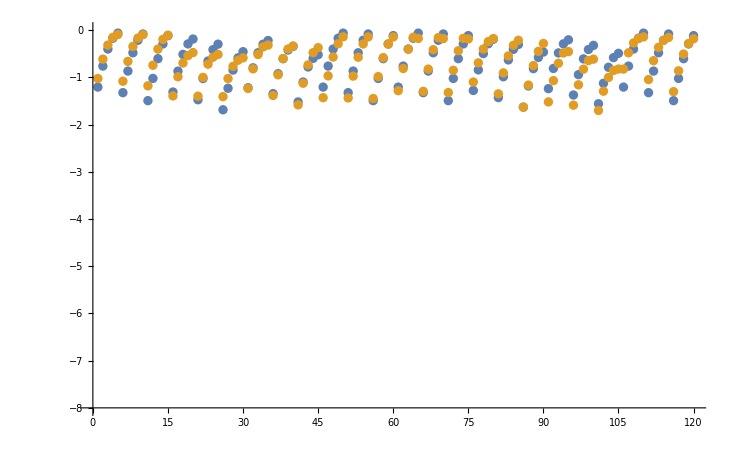

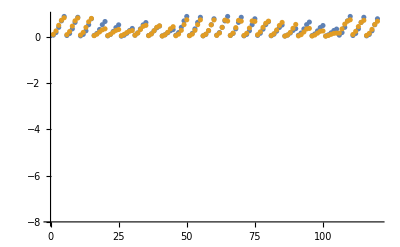

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

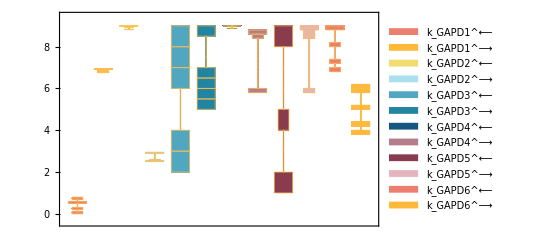

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

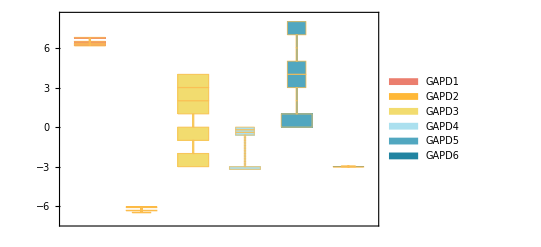

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

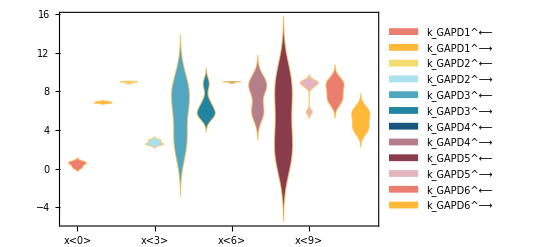

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

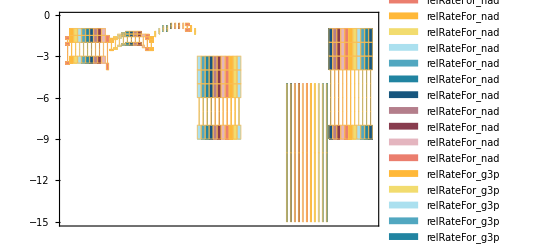

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= Underscript[E_total, Global]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.46352×10^-10
0.00089 | 0.00089 | 1.3663×10^-9
0.00053 | 0.00053 | 2.89852×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268. | 268. | 8.12479×10^-10

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 4.86486×10^-10